## New CA Classifiers (random colours)

### Wolfram Classes of ECAs

```mathematica
CAclasses = {1,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,3,2,2,2,3,2,2,2,2,2,2,2,3,2,1,2,2,2,2,2,2,2,1,3,2,2,2,3,2,2,2,2,2,2,2,2,4,2,2,2,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,3,2,2,3,3,2,2,2,2,2,1,3,2,2,2,3,3,2,2,3,3,3,2,2,4,2,2,2,2,2,2,2,2,2,3,3,3,2,4,2,3,2,1,3,2,2,2,2,2,3,1,4,2,2,2,2,2,2,2,2,3,4,2,3,3,3,2,3,2,2,2,2,2,2,1,3,2,2,2,3,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,2,2,2,2,2,2,1,4,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,1,1,2,2,1,1,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1};
```

### Functions for creating net and random datasets (ECAs, all 4 classes)

```mathematica
RandomRuleC[n_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[n,RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
netC[W_Integer,H_Integer]:=NetInitialize@NetChain[{ConvolutionLayer[16,{2,3}],Ramp,PoolingLayer[{H,W}-{1,2}],FlattenLayer[],LinearLayer[256],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[0,255]}]]
netTwoCC[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{2,4}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
dataC[W_Integer,H_Integer,n_Integer]:=Table[RandomRuleC[i,W,H]->CAclasses[[i+1]],{i,RandomChoice[Range[0,255],n]}]
```

```mathematica
netThreeCC[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"conv3"->ConvolutionLayer[16,{2,3}],"ramp3"->Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netThreeCC1024[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"conv3"->ConvolutionLayer[16,{2,3}],"ramp3"->Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 1024,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netFourCC512[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[32,{2,3}],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[32,{2,3}],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{2,4}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netFiveCC512[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[32,{2,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[32,{2,3}],"bat2"-> BatchNormalizationLayer[],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{2,4}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netSixCC512drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"drop1"->DropoutLayer[0.2],"conv1"-> ConvolutionLayer[32,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[32,{3,3}],"bat2"-> BatchNormalizationLayer[],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 512,"drop2"->DropoutLayer[0.2],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netSevenCC512drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[24,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[24,{3,3}],"bat2"-> BatchNormalizationLayer[],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 512,"drop2"->DropoutLayer[0.2],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netEightCC512drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[24,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[16,{2,3}],"bat2"->BatchNormalizationLayer[],"ramp2"-> Ramp, "conv3"-> ConvolutionLayer[24,{3,3}],"bat3"-> BatchNormalizationLayer[],"ramp3"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{8,16}],"flatten"-> FlattenLayer[],"linear"-> 1024,"drop2"->DropoutLayer[0.2],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netNineCC512drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[24,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[24,{3,3}],"bat2"->BatchNormalizationLayer[],"ramp2"-> Ramp, "conv3"-> ConvolutionLayer[24,{3,3}],"bat3"-> BatchNormalizationLayer[],"ramp3"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{12,12}],"flatten"-> FlattenLayer[],"linear"-> 512,"drop2"->DropoutLayer[0.2],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netTenCC1024drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[24,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[24,{3,3}],"bat2"->BatchNormalizationLayer[],"ramp2"-> Ramp, "conv3"-> ConvolutionLayer[24,{3,3}],"bat3"-> BatchNormalizationLayer[],"ramp3"-> Ramp,"conv4"-> ConvolutionLayer[24,{3,3}],"bat4"-> BatchNormalizationLayer[],"ramp4"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{12,12}],"flatten"-> FlattenLayer[],"linear"-> 1024,"drop2"->DropoutLayer[0.3],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netElevenCC1024drop[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[48,{3,3}],"bat1"-> BatchNormalizationLayer[],"ramp1"-> Ramp, "pooling1"-> PoolingLayer[{2,2}],"conv2"-> ConvolutionLayer[24,{3,3}],"bat2"->BatchNormalizationLayer[],"ramp2"-> Ramp, "pooling2"-> PoolingLayer[{2,2}],"conv3"-> ConvolutionLayer[24,{3,3}],"bat3"-> BatchNormalizationLayer[],"ramp3"-> Ramp,"pooling3"->PoolingLayer[{2,2}],"conv4"-> ConvolutionLayer[12,{3,3}],"bat4"-> BatchNormalizationLayer[],"ramp4"-> Ramp,"pooling4"-> PoolingLayer[{2,2}],"flatten"-> FlattenLayer[],"linear"-> 1024,"drop2"->DropoutLayer[0.3],"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

### Functions for creating datasets (1D totalistic CAs)

#### k=3, r=1 totalistic (class 4 only)

```mathematica
gen3TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {3,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data3T2C[W_Integer,H_Integer,n_Integer]:=Table[gen3TC[i,W,H]->4,{i,RandomChoice[{1635,1815,2007,2043,2049,1388,1041},n]}]
```

#### k=4, r=1 totalistic (class 4 only, 1 example)

```mathematica
gen4TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data4TC[W_Integer,H_Integer,n_Integer]:=Table[gen4TC[1004600,W,H]->4,n]
```

#### k=2, r=2 totalistic (all 4 classes)

```mathematica
gen2r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {2,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data2r2c4C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->4,{i,RandomChoice[{20,52},n]}]
data2r2c3C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->3,{i,RandomChoice[{2,6,10,12,14,18,22,26,28,30,34,38,42,44,46,50},n]}]
data2r2c2C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->2,{i,RandomChoice[{8,24,56},n]}]
data2r2c1C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->1,{i,RandomChoice[{0,4,16,32,36,40,48,54,58,60,62},n]}]
genData2r2C[W_Integer,H_Integer,n_Integer]:=Join[data2r2c4C[W,H,n], data2r2c3C[W,H,n],data2r2c2C[W,H,n],data2r2c1C[W,H,n]]
```

#### k=5, r=1 totalistic (class 4 only)

```mathematica
gen5T4C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data5T4C[n_Integer,W_Integer,H_Integer]:=Table[gen5T4C[i,W,H]->4,{i,RandomChoice[{781130654,772514435,1151319452,309095787,880862046,973835714,779446817,345466505,535500975,793363571,1052373865,455984785,339227109,1050973846,513368817,91315820,113925357},n]}]
```

### k=5, r=1 totalistic (classes 2/3/4)

```mathematica
gen5TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data5T4CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->4,{i,RandomChoice[{644218533,491739943,6889640,986144962,1099816682,988971204,300829994,272622024,304100638,626595633},n]}]
data5T3CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->3,{i,RandomChoice[{889082395,541068260,807907479,816180062,650485139,643827745,753940864,871525323,351440311,83501460},n]}]
data5T2CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->2,{i,RandomChoice[{525735659,1022330944,1007796739,495633437,1036827943},n]}]
genData5TCC[W_Integer,H_Integer,n_Integer]:=Join[data5T4CC[W,H,n], data5T3CC[W,H,n],data5T2CC[W,H,n]]
```

### Generate test datasets

#### k=2, r=2 non-totalistic

```mathematica
genk2r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, 2,2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak2r2C[W_Integer,H_Integer,n_Integer]:=Table[genk2r2C[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

#### k=2, r=3 non-totalistic

```mathematica
genk2r3NT[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, 2,3},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak2r3NT[W_Integer,H_Integer,n_Integer]:=Table[genk2r3NT[i,W,H]->i,{i,RandomInteger[2^2^7-1,n]}]
```

#### k=3, r=1 non-totalistic

```mathematica
genk3r1NT[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, 3},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak3r1NT[W_Integer,H_Integer,n_Integer]:=Table[genk3r1NT[i,W,H]->i,{i,RandomInteger[3^3^3-1,n]}]
```

#### k=3, r=2 totalistic

```mathematica
genk3r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {3,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak3r2C[W_Integer,H_Integer,n_Integer]:=Table[genk3r2C[i,W,H]->i,{i,RandomChoice[Range[0,177146],n]}]
```

#### k=3, r=3 totalistic

```mathematica
genk3r3C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {3,1},3},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak3r3C[W_Integer,H_Integer,n_Integer]:=Table[genk3r3C[i,W,H]->i,{i,RandomChoice[Range[0,14348906],n]}]
```

#### k=4, r=1 non-totalistic

```mathematica
genk4r1NT[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, 4},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak4r1NT[W_Integer,H_Integer,n_Integer]:=Table[genk4r1NT[i,W,H]->i,{i,RandomInteger[4^4^3-1,n]}]
```

#### k=4, r=1 totalistic

```mathematica
genk4r1C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak4r1C[W_Integer,H_Integer,n_Integer]:=Table[genk4r1C[i,W,H]->i,{i,RandomChoice[Range[0,1048575],n]}]
```

#### k=4, r=2 totalistic

```mathematica
genk4r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
datak4r2C[W_Integer,H_Integer,n_Integer]:=Table[genk4r2C[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

#### k=5, r=1 totalistic

```mathematica
gen5T2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data5T2C[n_Integer,W_Integer,H_Integer]:=Table[gen5T2C[i,W,H]->i,{i,RandomChoice[Range[0,1220703125],n]}]
```

#### k=6, r=1 totalistic

```mathematica
gen6TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {6,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data6TC[n_Integer,W_Integer,H_Integer]:=Table[gen6TC[i,W,H]->i,{i,RandomInteger[2821109907455,n]}]
```

#### k=6, r=2 totalistic

```mathematica
gen6T2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {6,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data6T2C[n_Integer,W_Integer,H_Integer]:=Table[gen6T2C[i,W,H]->i,{i,RandomInteger[170581728179578208255,n]}]
```

### k=7, r=1 totalistic

```mathematica
gen7TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {7,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data7TC[n_Integer,W_Integer,H_Integer]:=Table[gen7TC[i,W,H]->i,{i,RandomInteger[11398895185373142,n]}]
```

### k=8, r=1 totalistic

```mathematica
gen8TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {8,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data8TC[n_Integer,W_Integer,H_Integer]:=Table[gen8TC[i,W,H]->i,{i,RandomInteger[73786976294838206463,n]}]
```

### k=8, r=2 totalistic

```mathematica
gen8T2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {8,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[]},Frame->False]]
data8T2C[n_Integer,W_Integer,H_Integer]:=Table[gen8T2C[i,W,H]->i,{i,RandomInteger[324518553658426726783156020576255,n]}]
```

### k=9, r=1 totalistic

```mathematica
gen9TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {9,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{0->RandomColor[], 1->RandomColor[],3->RandomColor[],4->RandomColor[],5->RandomColor[],6->RandomColor[],7->RandomColor[],8->RandomColor[]},Frame->False]]
data9TC[n_Integer,W_Integer,H_Integer]:=Table[gen9TC[i,W,H]->i,{i,RandomInteger[717897987691852588770248,n]}]
```

### Network XIII - Two convolutions, dropout on linear only, BatchNorm

```mathematica
netECA13=netSevenCC512drop[128,128]
```

NetChain[<>]

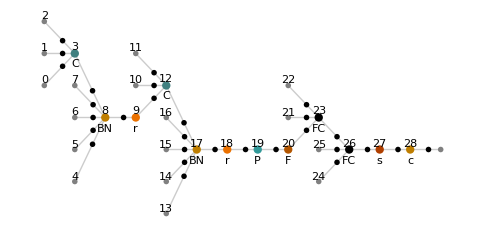

```mathematica
NetInformation[netECA13,"MXNetNodeGraphPlot"]
```

```mathematica
NetInformation[netECA13,"SummaryGraphic"]
```

-Graphics-

```mathematica
dataECA13=dataC[128,128,8192];
```

```mathematica
dataTotalistic2BigC13=genData2r2C[128,128,1024];
```

```mathematica
dataTotalistic3BigC13=data3T2C[128,128,1024];
```

```mathematica
dataTotalistic4BigC13=data4TC[128,128,1024];
```

```mathematica
dataTotalistic5BigC13=genData5TCC[128,128,4096];
```

```mathematica
fullTrainingBigC13=Join[dataECA13,dataTotalistic2BigC13,dataTotalistic3BigC13,dataTotalistic4BigC13,dataTotalistic5BigC13];
Length[fullTrainingBigC13]
```

26624

```mathematica
RandomSample[fullTrainingBigC13,20]
```

{-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→1,-Graphics-→3,-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→4}

```mathematica
RandomSample[fullTrainingBigC13,20]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1}

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA12=Import["netECA12-r12.wlnet"]
```

NetChain[<>]

```mathematica
netECA13=NetTrain[netECA13,fullTrainingBigC13,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

```mathematica
netECA13=Import["netECA13-r20.wlnet"]
```

NetChain[<>]

```mathematica
netECA13=NetTrain[netECA13,fullTrainingBigC13,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

### Generate test data for Network XIII

```mathematica
testDataECABigC=dataC[128,128,1024];
testData2TBigC=genData2r2C[128,128,1024];
testData3TBigC=data3T2C[128,128,1024];
testData4TBigC=data4TC[128,128,1024];
testData5TBigC=genData5TCC[128,128,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

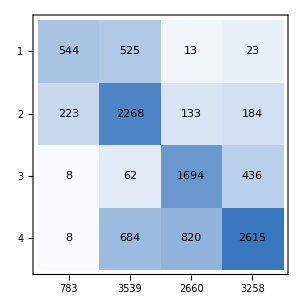
{0.69541,<|1→0.694764,2→0.640859,3→0.636842,4→0.80264|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA13, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA13[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA13[highEntBigC]]
Thread[lowEntBigC->netECA13[lowEntBigC]]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→4}

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

### Network XIV - BatchNorm, 1024 linear, dropout

```mathematica
netECA14=netEightCC512drop[128,128]
```

NetChain[<>]

```mathematica
netECA14=NetTrain[netECA14,fullTrainingBigC13,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA14=Import["netECA14-r20.wlnet"]
```

NetChain[<>]

### Generating test data for Network XIV

```mathematica
testDataECABigC=dataC[128,128,1024];
testData2TBigC=genData2r2C[128,128,1024];
testData3TBigC=data3T2C[128,128,1024];
testData4TBigC=data4TC[128,128,1024];
testData5TBigC=genData5TCC[128,128,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→4}

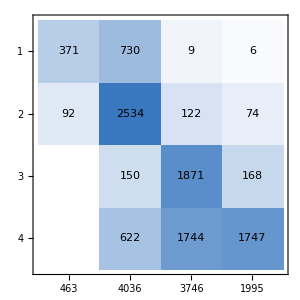
{0.637012,<|1→0.801296,2→0.627849,3→0.499466,4→0.875689|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA14, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA14[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA14[highEntBigC]]
Thread[lowEntBigC->netECA14[lowEntBigC]]
```

{-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→3}

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

### Network XV - Transfer learning with pre-trained image recognition net (VGG-16)

```mathematica
netECA15=NetModel["VGG-16 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
subNet=NetTake[netECA15,{"conv1_1","flatten_0"}]
```

NetChain[<>]

```mathematica
joinedNet=NetJoin[subNet,NetChain@<|"linear_new"->LinearLayer[1024],"linear_out"->LinearLayer[4],"prob"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

NetChain[<>]

```mathematica
netECA15final=NetPrepend[joinedNet,{"augment"->ImageAugmentationLayer[{224,224}]},"Input"->NetExtract[joinedNet,"Input"]]
```

NetChain[<>]

```mathematica
dataECA15=dataC[224,224,8192];
```

```mathematica
dataTotalistic2BigC15=genData2r2C[224,224,1024];
```

```mathematica
dataTotalistic3BigC15=data3T2C[224,224,512];
```

```mathematica
dataTotalistic4BigC15=data4TC[224,224,512];
```

```mathematica
dataTotalistic5BigC15=genData5TCC[224,224,1024];
```

```mathematica
fullTrainingBigC15=Join[dataECA15,dataTotalistic2BigC15,dataTotalistic3BigC15,dataTotalistic4BigC15,dataTotalistic5BigC15];
Length[fullTrainingBigC15]
```

16384

```mathematica
RandomSample[fullTrainingBigC15,20]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→1,-Graphics-→2}

```mathematica
netECA15final=NetTrain[netECA15final,fullTrainingBigC15,MaxTrainingRounds->5,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir},LearningRateMultipliers->{"linear_new"->1,"linear_out"->1,_->0}]
```

### Network XVI - Three convolutions, dropout on linear only, BatchNorm

```mathematica
netECA16=netNineCC512drop[128,128]
```

NetChain[<>]

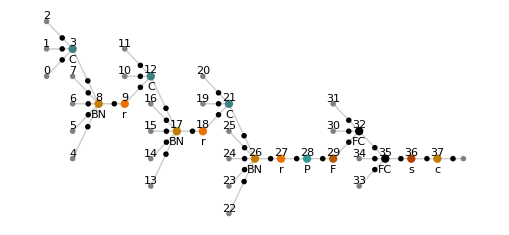

```mathematica
NetInformation[netECA16,"MXNetNodeGraphPlot"]
```

```mathematica
NetInformation[netECA16,"SummaryGraphic"]
```

-Graphics-

```mathematica
dataECA16=dataC[128,128,8192];
```

```mathematica
dataTotalistic2BigC16=genData2r2C[128,128,1024];
```

```mathematica
dataTotalistic3BigC16=data3T2C[128,128,1024];
```

```mathematica
dataTotalistic4BigC16=data4TC[128,128,1024];
```

```mathematica
dataTotalistic5BigC16=genData5TCC[128,128,4096];
```

```mathematica
fullTrainingBigC16=Join[dataECA16,dataTotalistic2BigC16,dataTotalistic3BigC16,dataTotalistic4BigC16,dataTotalistic5BigC16];
Length[fullTrainingBigC16]
```

26624

```mathematica
RandomSample[fullTrainingBigC16,20]
```

{-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→4}

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/home/esilverman/Documents

```mathematica
netECA16=NetTrain[netECA16,fullTrainingBigC16,MaxTrainingRounds->200,BatchSize->256,TargetDevice->"GPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

```mathematica
netECA16=Import["netECA16-r20.wlnet"]
```

```mathematica
netECA16=NetTrain[netECA16,fullTrainingBigC16,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

### Generate test data for Network XVI

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA16=Import["netECA16-r20.wlnet"]
```

NetChain[<>]

```mathematica
testDataECABigC=dataC[128,128,1024];
testData2TBigC=genData2r2C[128,128,1024];
testData3TBigC=data3T2C[128,128,1024];
testData4TBigC=data4TC[128,128,1024];
testData5TBigC=genData5TCC[128,128,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

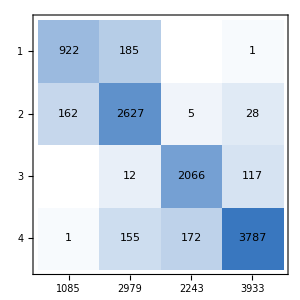
{0.918164,<|1→0.84977,2→0.88184,3→0.921088,4→0.962878|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA16, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA16[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA16[highEntBigC]]
Thread[lowEntBigC->netECA16[lowEntBigC]]
```

{-Graphics-→1,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→4}

{-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2}

### Testing Network XVI on unseen CA rule spaces

#### 2-colour non-totalistic, range 2

```mathematica
test4Data2kr2C16 = datak2r2C[128,128,8];
Thread[test4Data2kr2C16->netECA16[Keys@test4Data2kr2C16,{"TopProbabilities",2}]]
```

{(-Graphics-→142978078)→{4→0.0000385332,3→0.999961},(-Graphics-→2651048833)→{4→8.69455×10^-12,2→1.},(-Graphics-→2132867963)→{4→2.86202×10^-17,2→1.},(-Graphics-→3644758968)→{4→6.11899×10^-7,3→0.999999},(-Graphics-→1762420096)→{1→2.34707×10^-9,2→1.},(-Graphics-→1983429391)→{4→0.0547227,3→0.945277},(-Graphics-→3013553323)→{3→0.0109364,2→0.989064},(-Graphics-→4222841103)→{4→0.406794,3→0.593206}}

#### 2-colour non-totalistic, range 3

```mathematica
test4Data2kr3C16 = datak2r3NT[128,128,8];
Thread[test4Data2kr3C16->netECA16[Keys@test4Data2kr3C16,{"TopProbabilities",2}]]
```

{(-Graphics-→326920608662421742840307341423521605984)→{4→0.250823,3→0.749175},(-Graphics-→207378363536986723396466725374349770886)→{4→3.99297×10^-14,3→1.},(-Graphics-→208879936260575914948311642807908540203)→{4→1.58015×10^-11,3→1.},(-Graphics-→287306647832264924895832728648359695369)→{4→1.21845×10^-8,3→1.},(-Graphics-→229589239336289801086527228211518173928)→{3→0.0173989,4→0.982601},(-Graphics-→25263864036549856421518677057185002153)→{4→2.486×10^-11,3→1.},(-Graphics-→122573209377430367268072050742932826218)→{4→1.46881×10^-9,3→1.},(-Graphics-→120291014848530508056036077228147332137)→{4→0.00683298,3→0.993167}}

#### 3-colour non-totalistic, range 1

```mathematica
test4Data3kr1C16 = datak3r1NT[128,128,8];
Thread[test4Data3kr1C16->netECA16[Keys@test4Data3kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→4431477695805)→{4→0.000746188,3→0.999254},(-Graphics-→1627958441874)→{4→0.00025369,3→0.999746},(-Graphics-→4241674451024)→{3→0.194892,2→0.805108},(-Graphics-→4177916755057)→{3→9.07174×10^-18,4→1.},(-Graphics-→2504235138103)→{4→1.3375×10^-21,2→1.},(-Graphics-→2281646033785)→{4→0.164883,3→0.835117},(-Graphics-→886946817375)→{2→0.000352038,1→0.999648},(-Graphics-→1468391136669)→{4→1.85451×10^-11,2→1.}}

#### 3-colour totalistic, range 2

```mathematica
test4Data3kr2C16 = datak3r2C[128,128,8];
Thread[test4Data3kr2C16->netECA16[Keys@test4Data3kr2C16,{"TopProbabilities",2}]]
```

{(-Graphics-→31794)→{2→0.0000274564,1→0.999973},(-Graphics-→154722)→{4→3.53893×10^-6,3→0.999996},(-Graphics-→47093)→{3→0.0000226662,4→0.999977},(-Graphics-→40833)→{2→7.38958×10^-10,1→1.},(-Graphics-→70499)→{4→9.14168×10^-7,3→0.999999},(-Graphics-→104031)→{2→0.00469642,1→0.995304},(-Graphics-→102416)→{4→0.00127827,3→0.998722},(-Graphics-→143812)→{3→0.00152229,4→0.998478}}

#### 3-colour totalistic, range 3

```mathematica
test4Data3kr3C16 = datak3r3C[128,128,8];
Thread[test4Data3kr3C16->netECA16[Keys@test4Data3kr3C16,{"TopProbabilities",2}]]
```

{(-Graphics-→9694493)→{3→0.480724,4→0.519276},(-Graphics-→1266350)→{3→2.07073×10^-17,4→1.},(-Graphics-→10922251)→{4→0.0000302967,3→0.99997},(-Graphics-→10284081)→{4→0.0000121386,3→0.999988},(-Graphics-→3664255)→{1→0.0137727,2→0.986227},(-Graphics-→10298881)→{4→0.000133186,3→0.999867},(-Graphics-→8621297)→{3→5.17911×10^-10,4→1.},(-Graphics-→11392150)→{4→8.14877×10^-14,3→1.}}

#### 4-colour non-totalistic, range 1

```mathematica
test4Data4kr1C16 = datak4r1NT[128,128,8];
Thread[test4Data4kr1C16->netECA16[Keys@test4Data4kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→154080220988097676666997866552654645473)→{3→2.29402×10^-6,4→0.999998},(-Graphics-→23699455383307433676732305926546946154)→{4→9.18698×10^-10,3→1.},(-Graphics-→128473503291830537978738932215015934320)→{4→0.016884,3→0.983116},(-Graphics-→229632577374973873063824352556638470668)→{3→3.66751×10^-6,4→0.999996},(-Graphics-→296751325089499848049286011129052334280)→{2→0.0356663,4→0.964334},(-Graphics-→58389931388288805968545394973250265077)→{4→0.392533,3→0.607467},(-Graphics-→190838234746017730793117442629783928461)→{3→0.0000369307,4→0.999963},(-Graphics-→203920243365735713208234812082196839807)→{4→0.00577653,3→0.994223}}

#### 4-colour totalistic, range 2

```mathematica
test4Data4kr2C16 = datak4r2C[128,128,8];
Thread[test4Data4kr2C16->netECA16[Keys@test4Data4kr2C16,{"TopProbabilities",2}]]
```

{(-Graphics-→25517204)→{4→1.29127×10^-13,3→1.},(-Graphics-→3053925273)→{4→0.00215091,3→0.997849},(-Graphics-→2735868989)→{4→0.000282149,3→0.999718},(-Graphics-→1440927950)→{4→0.0889018,3→0.911098},(-Graphics-→3727816705)→{3→2.78599×10^-7,4→1.},(-Graphics-→818963457)→{4→4.45422×10^-19,3→1.},(-Graphics-→3948742311)→{4→2.06369×10^-10,3→1.},(-Graphics-→1159108912)→{4→0.431018,2→0.568975}}

#### 5-colour totalistic, range 1

```mathematica
test4Data5kr1C16 = data5T2C[8,128,128];
Thread[test4Data5kr1C16->netECA16[Keys@test4Data5kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→81353109)→{4→4.44391×10^-7,2→1.},(-Graphics-→626536724)→{3→3.46291×10^-8,4→1.},(-Graphics-→129595314)→{4→0.00257287,3→0.997427},(-Graphics-→513885470)→{1→1.41572×10^-11,2→1.},(-Graphics-→494894021)→{3→0.0136503,4→0.98635},(-Graphics-→459414632)→{4→0.0000813289,3→0.999919},(-Graphics-→327281621)→{4→2.29489×10^-8,3→1.},(-Graphics-→503044041)→{4→0.191949,3→0.808051}}

#### 6-colour totalistic, range 1

```mathematica
test4Data6kr1C16 = data6TC[8,128,128];
Thread[test4Data6kr1C16->netECA16[Keys@test4Data6kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→1522715109251)→{4→2.02852×10^-8,3→1.},(-Graphics-→1026953898330)→{4→2.88279×10^-8,3→1.},(-Graphics-→1583652682)→{3→0.429972,4→0.570028},(-Graphics-→2123073201165)→{4→6.23239×10^-10,3→1.},(-Graphics-→341591565791)→{4→0.00212154,3→0.997878},(-Graphics-→2568539246083)→{4→0.00197237,3→0.998028},(-Graphics-→1213730554155)→{4→0.0020281,3→0.997972},(-Graphics-→389841312036)→{4→2.91693×10^-11,3→1.}}

#### 6-colour totalistic, range 2

```mathematica
test4Data6kr2C16 = data6T2C[8,128,128];
Thread[test4Data6kr2C16->netECA16[Keys@test4Data6kr2C16,{"TopProbabilities",2}]]
```

{(-Graphics-→46177535535728053148)→{4→6.75757×10^-8,3→1.},(-Graphics-→35643164656729746413)→{4→4.68349×10^-15,3→1.},(-Graphics-→151294335263255298785)→{4→0.0673459,3→0.932654},(-Graphics-→8803703818914948546)→{4→0.00560205,3→0.994398},(-Graphics-→46723275025483150950)→{4→0.00307226,3→0.996928},(-Graphics-→72312079279485910528)→{4→0.00153324,3→0.998467},(-Graphics-→22158237683799083047)→{4→3.51784×10^-13,3→1.},(-Graphics-→142446781366136429283)→{4→3.01302×10^-11,3→1.}}

#### 7-colour totalistic, range 1

```mathematica
test4Data7kr1C16 = data7TC[8,128,128];
Thread[test4Data7kr1C16->netECA16[Keys@test4Data7kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→3109608593887262)→{2→0.0267983,4→0.973202},(-Graphics-→10516337788191339)→{4→0.202783,3→0.797217},(-Graphics-→10218434972470056)→{4→2.59313×10^-9,3→1.},(-Graphics-→11301098979433534)→{4→5.31247×10^-20,3→1.},(-Graphics-→4222218586098008)→{4→2.3505×10^-8,3→1.},(-Graphics-→6272918110265620)→{4→2.82334×10^-12,3→1.},(-Graphics-→7237960144206103)→{4→1.82804×10^-11,3→1.},(-Graphics-→8157411943012914)→{4→7.30163×10^-8,3→1.}}

```mathematica
test4Data7kr1C16 = data7TC[8,128,128];
Thread[test4Data7kr1C16->netECA16[Keys@test4Data7kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→2054187704193738)→{2→1.00393×10^-7,1→1.},(-Graphics-→4502314670347259)→{1→0.000272502,2→0.999727},(-Graphics-→6433286718439853)→{4→3.57308×10^-13,3→1.},(-Graphics-→10115271094201812)→{4→1.83956×10^-14,3→1.},(-Graphics-→2056629839849700)→{4→7.03567×10^-6,2→0.999993},(-Graphics-→6016684767156829)→{4→0.0021258,3→0.997874},(-Graphics-→1150898749617983)→{4→5.05985×10^-9,3→1.},(-Graphics-→3441885208643463)→{3→1.57168×10^-8,2→1.}}

```mathematica
test4Data7kr1C16 = data7TC[8,128,128];
Thread[test4Data7kr1C16->netECA16[Keys@test4Data7kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→8718538805570808)→{4→0.0199047,2→0.980095},(-Graphics-→5687458247703346)→{3→3.931×10^-6,4→0.999995},(-Graphics-→2004300484518722)→{3→0.0438658,4→0.956134},(-Graphics-→2106485862858275)→{4→3.36807×10^-10,3→1.},(-Graphics-→10335102717390268)→{4→1.40275×10^-9,2→1.},(-Graphics-→1948304137097478)→{4→3.0757×10^-6,3→0.999997},(-Graphics-→742855573082935)→{3→0.00423487,4→0.995765},(-Graphics-→550991988954034)→{3→0.0000158322,4→0.999984}}

#### 8-colour totalistic, range 1

```mathematica
test4Data8kr1C16 = data8TC[8,128,128];
Thread[test4Data8kr1C16->netECA16[Keys@test4Data8kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→26660220729300317631)→{3→4.53753×10^-16,4→1.},(-Graphics-→57706619077455169987)→{4→0.00012086,3→0.999879},(-Graphics-→64248301738433598883)→{4→8.62498×10^-7,3→0.999999},(-Graphics-→38309191234358472181)→{3→0.0920227,4→0.907977},(-Graphics-→10057418236647939786)→{3→0.00153869,4→0.998461},(-Graphics-→55038816396722824044)→{4→7.93818×10^-11,3→1.},(-Graphics-→13857790822319662750)→{4→1.6375×10^-9,2→1.},(-Graphics-→35001739471058241746)→{3→0.146189,4→0.853811}}

```mathematica
test4Data8kr1C16 = data8TC[8,128,128];
Thread[test4Data8kr1C16->netECA16[Keys@test4Data8kr1C16,{"TopProbabilities",2}]]
```

{(-Graphics-→8889571206431822669)→{4→7.71651×10^-13,3→1.},(-Graphics-→12932107158159577869)→{4→0.000487127,3→0.999513},(-Graphics-→38300014541797689408)→{2→4.40131×10^-9,4→1.},(-Graphics-→73619662786582031542)→{4→2.6954×10^-22,3→1.},(-Graphics-→25075664454379326631)→{4→2.7484×10^-6,3→0.999997},(-Graphics-→66251301754800867134)→{4→0.045885,3→0.954115},(-Graphics-→45939929171629412480)→{3→0.0015837,4→0.998416},(-Graphics-→48918067825593479863)→{4→0.000601606,3→0.999398}}

### Network XVII - Four convolutions, dropout on linear only, BatchNorm

```mathematica
netECA17=netTenCC1024drop[128,128]
```

NetChain[<>]

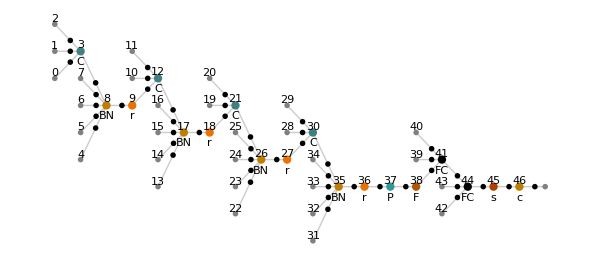

```mathematica
NetInformation[netECA17,"MXNetNodeGraphPlot"]
```

```mathematica
NetInformation[netECA17,"SummaryGraphic"]
```

-Graphics-

```mathematica
dataECA17=dataC[128,128,16384];
```

```mathematica
dataTotalistic2BigC17=genData2r2C[128,128,2048];
```

```mathematica
dataTotalistic3BigC17=data3T2C[128,128,2048];
```

```mathematica
dataTotalistic4BigC17=data4TC[128,128,2048];
```

```mathematica
dataTotalistic5BigC17=genData5TCC[128,128,8192];
```

```mathematica
fullTrainingBigC17=Join[dataECA17,dataTotalistic2BigC17,dataTotalistic3BigC17,dataTotalistic4BigC17,dataTotalistic5BigC17];
Length[fullTrainingBigC17]
```

53248

```mathematica
RandomSample[fullTrainingBigC17,20]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→2}

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

```mathematica
"/home/esilverman/Documents"
```

/home/esilverman/Documents

```mathematica
netECA17=NetTrain[netECA17,fullTrainingBigC17,MaxTrainingRounds->200,BatchSize->256,TargetDevice->"GPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

```mathematica
netECA17=Import["netECA17-r200.wlnet"]
```

### Generate test data for Network XVII (200 epochs)

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA17=Import["netECA17-r200.wlnet"]
```

NetChain[<>]

```mathematica
testDataECABigC=dataC[128,128,1024];
testData2TBigC=genData2r2C[128,128,1024];
testData3TBigC=data3T2C[128,128,1024];
testData4TBigC=data4TC[128,128,1024];
testData5TBigC=genData5TCC[128,128,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2}

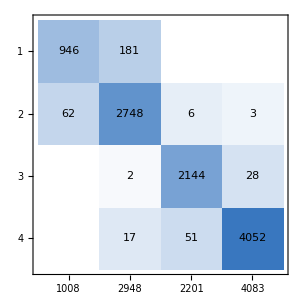
{0.96582,<|1→0.938492,2→0.932157,3→0.974103,4→0.992408|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA17, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA17[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA17[highEntBigC]]
Thread[lowEntBigC->netECA17[lowEntBigC]]
```

{-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→3,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→3}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3}

### Testing Network XVII (200 epochs) on unseen CA rule spaces

#### 2-colour non-totalistic, range 2

```mathematica
test4Data2kr2C17 = datak2r2C[128,128,8];
Thread[test4Data2kr2C17->netECA17[Keys@test4Data2kr2C17,{"TopProbabilities",2}]]
```

{(-Graphics-→3594886935)→{3→1.19587×10^-7,2→1.},(-Graphics-→4012014789)→{4→0.00317589,3→0.996824},(-Graphics-→736342145)→{4→0.000138652,3→0.999861},(-Graphics-→3597938931)→{4→5.42024×10^-16,2→1.},(-Graphics-→49406137)→{1→4.03179×10^-30,2→1.},(-Graphics-→669500034)→{4→0.0129747,2→0.983657},(-Graphics-→4122605661)→{1→6.18382×10^-9,2→1.},(-Graphics-→2751618302)→{4→5.91412×10^-9,3→1.}}

#### 2-colour non-totalistic, range 3

```mathematica
test4Data2kr3C17 = datak2r3NT[128,128,8];
Thread[test4Data2kr3C17->netECA17[Keys@test4Data2kr3C17,{"TopProbabilities",2}]]
```

{(-Graphics-→34540309799423528179267302306223835543)→{4→0.0000190167,3→0.999981},(-Graphics-→271913994962168934532188611494783284369)→{4→8.79258×10^-15,3→1.},(-Graphics-→328899203265424040719063648351222904052)→{3→0.000609094,4→0.999391},(-Graphics-→193952196319600964880345641761505849023)→{4→8.96571×10^-10,3→1.},(-Graphics-→196656308173162097107061836715379270739)→{4→3.36397×10^-6,3→0.999997},(-Graphics-→26038517878084050104120010197636533172)→{3→5.4757×10^-7,4→0.999999},(-Graphics-→252109815601340225609723212759419626786)→{4→1.35911×10^-8,3→1.},(-Graphics-→306252930975464521922673887271988404115)→{4→5.68649×10^-7,3→0.999999}}

#### 3-colour non-totalistic, range 1

```mathematica
test4Data3kr1C17 = datak3r1NT[128,128,8];
Thread[test4Data3kr1C17->netECA17[Keys@test4Data3kr1C17,{"TopProbabilities",2}]]
```

{(-Graphics-→1924646489567)→{3→1.76606×10^-30,2→1.},(-Graphics-→3672534501071)→{2→0.0000110699,4→0.999989},(-Graphics-→5833330297781)→{2→0.000232935,4→0.999767},(-Graphics-→7606192973798)→{2→6.802×10^-10,1→1.},(-Graphics-→7622301560954)→{3→0.0391643,2→0.960836},(-Graphics-→3685910174297)→{3→2.7602×10^-8,4→1.},(-Graphics-→5743838876456)→{1→6.15406×10^-23,2→1.},(-Graphics-→3655040152191)→{4→0.0374305,3→0.962569}}

#### 3-colour totalistic, range 2

```mathematica
test4Data3kr2C17 = datak3r2C[128,128,8];
Thread[test4Data3kr2C17->netECA17[Keys@test4Data3kr2C17,{"TopProbabilities",2}]]
```

{(-Graphics-→43149)→{4→1.6989×10^-8,3→1.},(-Graphics-→160434)→{1→2.05354×10^-18,2→1.},(-Graphics-→9535)→{3→0.0000598239,4→0.99994},(-Graphics-→172239)→{1→0.00705153,2→0.992948},(-Graphics-→174680)→{2→5.824×10^-11,1→1.},(-Graphics-→55945)→{4→0.0138349,3→0.986165},(-Graphics-→113483)→{4→3.72822×10^-6,3→0.999996},(-Graphics-→67810)→{1→6.91386×10^-17,2→1.}}

#### 3-colour totalistic, range 3

```mathematica
test4Data3kr3C17 = datak3r3C[128,128,8];
Thread[test4Data3kr3C17->netECA17[Keys@test4Data3kr3C17,{"TopProbabilities",2}]]
```

{(-Graphics-→3046610)→{4→7.58312×10^-7,3→0.999999},(-Graphics-→7801434)→{1→1.19167×10^-14,2→1.},(-Graphics-→5445843)→{4→1.60992×10^-19,3→1.},(-Graphics-→1451413)→{4→0.144413,3→0.855587},(-Graphics-→10676790)→{3→0.0738921,4→0.926108},(-Graphics-→10375449)→{4→1.04031×10^-17,3→1.},(-Graphics-→5181761)→{4→1.75908×10^-8,3→1.},(-Graphics-→8884285)→{4→7.91486×10^-6,3→0.999992}}

#### 4-colour non-totalistic, range 1

```mathematica
test4Data4kr1C17 = datak4r1NT[128,128,8];
Thread[test4Data4kr1C17->netECA17[Keys@test4Data4kr1C17,{"TopProbabilities",2}]]
```

{(-Graphics-→255219118556246495764448982135818252673)→{3→2.62807×10^-6,4→0.999997},(-Graphics-→256372744774750994462308116064689670029)→{4→1.66442×10^-17,3→1.},(-Graphics-→287015413736003568798718608141279906438)→{4→2.56385×10^-7,3→1.},(-Graphics-→102047809483228794436919245364544665433)→{4→0.000696463,3→0.999304},(-Graphics-→240555046861732528519285194385835154772)→{4→3.62136×10^-16,3→1.},(-Graphics-→16370468900338540956022703184589781262)→{3→1.45252×10^-15,4→1.},(-Graphics-→121099422536966135180998722819969755137)→{4→0.0000270873,3→0.999973},(-Graphics-→264867193286423906380401526070744380919)→{4→0.105214,3→0.894786}}

#### 4-colour totalistic, range 2

```mathematica
test4Data4kr2C17= datak4r2C[128,128,8];
Thread[test4Data4kr2C17->netECA17[Keys@test4Data4kr2C17,{"TopProbabilities",2}]]
```

{(-Graphics-→616082315)→{4→8.8653×10^-10,3→1.},(-Graphics-→1568191428)→{4→5.21264×10^-11,3→1.},(-Graphics-→1216110065)→{4→0.000040346,3→0.99996},(-Graphics-→2419903949)→{4→3.69897×10^-10,3→1.},(-Graphics-→453961055)→{4→3.89961×10^-8,3→1.},(-Graphics-→3969029930)→{2→0.0000237283,4→0.999976},(-Graphics-→3970208335)→{4→4.03487×10^-9,3→1.},(-Graphics-→3418384250)→{4→9.0126×10^-15,3→1.}}

#### 5-colour totalistic, range 1

```mathematica
test4Data5kr1C17 = data5T2C[8,128,128];
Thread[test4Data5kr1C17->netECA17[Keys@test4Data5kr1C17,{"TopProbabilities",2}]]
```

{(-Graphics-→720503516)→{2→0.000105936,4→0.999894},(-Graphics-→771013684)→{4→1.94282×10^-8,2→1.},(-Graphics-→543872434)→{4→6.11423×10^-7,3→0.999999},(-Graphics-→341908586)→{4→0.310854,3→0.689146},(-Graphics-→664036861)→{2→0.00511847,4→0.994882},(-Graphics-→1182110899)→{4→0.039023,3→0.960977},(-Graphics-→976082949)→{4→9.09593×10^-19,2→1.},(-Graphics-→1019517181)→{1→6.47917×10^-10,2→1.}}

#### 6-colour totalistic, range 1

```mathematica
test4Data6kr1C17= data6TC[8,128,128];
Thread[test4Data6kr1C17->netECA17[Keys@test4Data6kr1C17,{"TopProbabilities",2}]]
```

{(-Graphics-→1128957409115)→{2→0.387573,1→0.612427},(-Graphics-→744151919694)→{3→1.28454×10^-11,4→1.},(-Graphics-→411482269593)→{4→9.50671×10^-6,3→0.99999},(-Graphics-→2122826252429)→{4→4.58698×10^-10,3→1.},(-Graphics-→2443710325124)→{4→5.97811×10^-9,3→1.},(-Graphics-→2519595515832)→{2→0.396179,4→0.603821},(-Graphics-→572558234379)→{4→1.63969×10^-11,3→1.},(-Graphics-→2103617145248)→{3→8.41391×10^-9,4→1.}}

#### 6-colour totalistic, range 2

```mathematica
test4Data6kr2C17 = data6T2C[8,128,128];
Thread[test4Data6kr2C17->netECA17[Keys@test4Data6kr2C17,{"TopProbabilities",2}]]
```

{(-Graphics-→56518611906036513420)→{4→0.00132297,3→0.998677},(-Graphics-→149111145742470978404)→{4→0.00110016,3→0.9989},(-Graphics-→60075298400874491559)→{4→0.0000816385,3→0.999918},(-Graphics-→61137219885741406688)→{4→6.01526×10^-9,3→1.},(-Graphics-→138083937800052503915)→{4→1.63338×10^-6,3→0.999998},(-Graphics-→102848890668267918696)→{4→4.51684×10^-8,3→1.},(-Graphics-→52002759529482240344)→{4→0.0161382,3→0.983862},(-Graphics-→3771326190903203597)→{4→1.57635×10^-10,3→1.}}

#### 7-colour totalistic, range 1

```mathematica
test4Data7kr1C17 = data7TC[8,128,128];
Thread[test4Data7kr1C17->netECA17[Keys@test4Data7kr1C17,{"TopProbabilities",2}]]
```

{(-Graphics-→249739897876317)→{4→7.58753×10^-13,3→1.},(-Graphics-→6589873174284234)→{4→3.70203×10^-21,3→1.},(-Graphics-→2838251451633386)→{3→0.0000362001,4→0.999964},(-Graphics-→3069021856393877)→{4→4.6982×10^-6,3→0.999995},(-Graphics-→10282712720317214)→{3→4.14045×10^-19,4→1.},(-Graphics-→203015413423084)→{4→2.87431×10^-9,3→1.},(-Graphics-→9746864148555591)→{3→1.53822×10^-7,4→1.},(-Graphics-→8003062538664128)→{3→2.05185×10^-8,4→1.}}

#### 8-colour totalistic, range 1

```mathematica
test4Data8kr1C17= data8TC[8,128,128];
Thread[test4Data8kr1C17->netECA17[Keys@test4Data8kr1C17,{"TopProbabilities",2}]]
```

{(-Graphics-→10266196594935096075)→{4→8.5791×10^-18,3→1.},(-Graphics-→731338973990773560)→{2→7.53019×10^-12,4→1.},(-Graphics-→11247173012174218620)→{4→0.0000380778,3→0.999962},(-Graphics-→63742472032617219918)→{4→0.0000371126,3→0.999963},(-Graphics-→7382455380800363015)→{4→8.07468×10^-15,3→1.},(-Graphics-→59100651667569734000)→{4→1.27228×10^-11,3→1.},(-Graphics-→24971306247396766335)→{4→0.0333734,3→0.966627},(-Graphics-→45946581080593555746)→{4→1.08598×10^-15,3→1.}}

```mathematica
test4Data8kr1C17= data8TC[8,128,128];
Thread[test4Data8kr1C17->netECA17[Keys@test4Data8kr1C17,{"TopProbabilities",2}]]
```

{(-Graphics-→14955350598586141683)→{4→1.70104×10^-7,3→1.},(-Graphics-→30727455169449395964)→{4→4.31945×10^-11,3→1.},(-Graphics-→42490152676883207115)→{3→0.0000793636,4→0.999921},(-Graphics-→18395296261071222192)→{4→0.0142026,3→0.985797},(-Graphics-→22317090484634250431)→{3→0.00783339,4→0.992167},(-Graphics-→33329414465629594174)→{4→0.00851294,3→0.991487},(-Graphics-→68439232681205604962)→{2→1.97568×10^-13,4→1.},(-Graphics-→53049830479062864751)→{4→3.6815×10^-10,3→1.}}

### Network XVIII- Four convolutions, dropout on linear only, BatchNorm

```mathematica
netECA18=netTenCC1024drop[128,128]
```

NetChain[<>]

```mathematica
NetInformation[netECA18,"MXNetNodeGraphPlot"]
```

-Graphics-

```mathematica
NetInformation[netECA18,"SummaryGraphic"]
```

-Graphics-

```mathematica
dataECA18=dataC[128,128,16384];
```

```mathematica
dataTotalistic2BigC18=genData2r2C[128,128,4096];
```

```mathematica
dataTotalistic3BigC18=data3T2C[128,128,4096];
```

```mathematica
dataTotalistic4BigC18=data4TC[128,128,4096];
```

```mathematica
dataTotalistic5BigC18=genData5TCC[128,128,16384];
```

```mathematica
fullTrainingBigC18=Join[dataECA18,dataTotalistic2BigC18,dataTotalistic3BigC18,dataTotalistic4BigC18,dataTotalistic5BigC18];
Length[fullTrainingBigC18]
```

90112

```mathematica
RandomSample[fullTrainingBigC18,20]
```

{-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→1,-Graphics-→4,-Graphics-→1}

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/home/esilverman/Documents

```mathematica
"/home/esilverman/Documents"
```

/home/esilverman/Documents

```mathematica
netECA18=NetTrain[netECA18,fullTrainingBigC18,MaxTrainingRounds->200,BatchSize->256,TargetDevice->"GPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

```mathematica
netECA18=Import["netECA18-r200.wlnet"]
```

NetChain[<>]

### Generate test data for Network XVII (200 epochs)

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA18=Import["netECA18-r200.wlnet"]
```

NetChain[<>]

```mathematica
testDataECABigC=dataC[128,128,1024];
testData2TBigC=genData2r2C[128,128,1024];
testData3TBigC=data3T2C[128,128,1024];
testData4TBigC=data4TC[128,128,1024];
testData5TBigC=genData5TCC[128,128,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2}

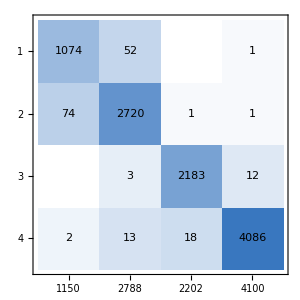
{0.982715,<|1→0.933913,2→0.97561,3→0.991371,4→0.996585|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA18, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA18[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA18[highEntBigC]]
Thread[lowEntBigC->netECA18[lowEntBigC]]
```

{-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→3}

{-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→2}

### Testing Network XVIII (200 epochs) on unseen CA rule spaces

#### 2-colour non-totalistic, range 2

```mathematica
test4Data2kr2C18= datak2r2C[128,128,8];
Thread[test4Data2kr2C18->netECA18[Keys@test4Data2kr2C18,{"TopProbabilities",2}]]
```

{(-Graphics-→104119361)→{2→0.0334506,4→0.966538},(-Graphics-→426073771)→{3→0.0891399,4→0.910856},(-Graphics-→1487290163)→{4→8.29353×10^-14,3→1.},(-Graphics-→3761497755)→{4→0.484906,3→0.514237},(-Graphics-→1503689727)→{3→6.00879×10^-8,4→1.},(-Graphics-→2106940334)→{4→5.44016×10^-23,3→1.},(-Graphics-→2590447558)→{4→2.78794×10^-8,3→1.},(-Graphics-→4213015958)→{1→2.47284×10^-12,2→1.}}

#### 2-colour non-totalistic, range 3

```mathematica
test4Data2kr3C18 = datak2r3NT[128,128,8];
Thread[test4Data2kr3C18->netECA18[Keys@test4Data2kr3C18,{"TopProbabilities",2}]]
```

{(-Graphics-→330416984885540388017354162041951825587)→{3→8.74296×10^-8,4→1.},(-Graphics-→279656361264376888074030685915728704181)→{4→0.0213521,3→0.978648},(-Graphics-→197632068292332388955030541940304062122)→{4→5.0499×10^-16,3→1.},(-Graphics-→188082660194176799122844083244865677445)→{4→2.34238×10^-6,3→0.999998},(-Graphics-→99467121511183621679443804486384512063)→{4→0.00329566,3→0.996704},(-Graphics-→56219309346455872630743597889899213800)→{4→1.38574×10^-10,3→1.},(-Graphics-→308130247560683500868656567738983907586)→{4→5.1263×10^-8,3→1.},(-Graphics-→333388526947822905616741326831869137342)→{4→7.10494×10^-8,3→1.}}

#### 3-colour non-totalistic, range 1

```mathematica
test4Data3kr1C18 = datak3r1NT[128,128,8];
Thread[test4Data3kr1C18->netECA18[Keys@test4Data3kr1C18,{"TopProbabilities",2}]]
```

{(-Graphics-→1592394332064)→{2→7.59314×10^-6,4→0.999992},(-Graphics-→4098174485356)→{4→8.44302×10^-20,2→1.},(-Graphics-→5930373291731)→{1→2.34989×10^-7,2→1.},(-Graphics-→6363744081807)→{3→0.0000390704,4→0.999961},(-Graphics-→1193083886293)→{4→0.0126455,3→0.987355},(-Graphics-→1957822902340)→{3→0.0000561806,2→0.999944},(-Graphics-→2179566018820)→{4→1.10915×10^-6,3→0.999999},(-Graphics-→4111476009175)→{4→1.84666×10^-16,3→1.}}

#### 3-colour totalistic, range 2

```mathematica
test4Data3kr2C18 = datak3r2C[128,128,8];
Thread[test4Data3kr2C18->netECA18[Keys@test4Data3kr2C18,{"TopProbabilities",2}]]
```

{(-Graphics-→101105)→{4→1.49159×10^-7,3→1.},(-Graphics-→48212)→{4→3.39887×10^-8,3→1.},(-Graphics-→81243)→{2→6.61823×10^-15,1→1.},(-Graphics-→144952)→{4→5.58692×10^-14,3→1.},(-Graphics-→167730)→{1→3.79715×10^-7,2→1.},(-Graphics-→102220)→{4→3.5215×10^-7,3→1.},(-Graphics-→129071)→{4→5.28522×10^-29,3→1.},(-Graphics-→94027)→{4→3.95426×10^-7,3→1.}}

#### 3-colour totalistic, range 3

```mathematica
test4Data3kr3C18 = datak3r3C[128,128,8];
Thread[test4Data3kr3C18->netECA18[Keys@test4Data3kr3C18,{"TopProbabilities",2}]]
```

{(-Graphics-→461960)→{4→4.84455×10^-6,3→0.999995},(-Graphics-→4823863)→{4→1.80913×10^-22,3→1.},(-Graphics-→7272180)→{3→3.43734×10^-9,4→1.},(-Graphics-→8672980)→{4→6.70981×10^-6,3→0.999993},(-Graphics-→254357)→{4→2.17773×10^-6,3→0.999998},(-Graphics-→9226537)→{4→1.70317×10^-12,3→1.},(-Graphics-→13913899)→{4→1.88245×10^-14,3→1.},(-Graphics-→2641642)→{4→1.17168×10^-16,3→1.}}

#### 4-colour non-totalistic, range 1

```mathematica
test4Data4kr1C18 = datak4r1NT[128,128,8];
Thread[test4Data4kr1C18->netECA18[Keys@test4Data4kr1C18,{"TopProbabilities",2}]]
```

{(-Graphics-→102061531028325101056411203373159921153)→{4→1.52655×10^-6,3→0.999998},(-Graphics-→220826430777843014546276939581509597468)→{4→3.71156×10^-15,3→1.},(-Graphics-→189759227742452338669016752488159725978)→{3→1.71606×10^-19,4→1.},(-Graphics-→39086343891936177646298077938677400893)→{4→0.0000617923,3→0.999938},(-Graphics-→325561419730770765208110988081624688453)→{4→4.25321×10^-7,3→1.},(-Graphics-→247405682417519114838497454468289242544)→{4→3.94091×10^-12,3→1.},(-Graphics-→173148209233830655560355066654224721166)→{4→1.19081×10^-14,3→1.},(-Graphics-→272790974570863467026653486918315112723)→{3→2.26679×10^-10,4→1.}}

#### 4-colour totalistic, range 2

```mathematica
test4Data4kr2C18= datak4r2C[128,128,8];
Thread[test4Data4kr2C18->netECA18[Keys@test4Data4kr2C18,{"TopProbabilities",2}]]
```

{(-Graphics-→3511876239)→{2→1.5807×10^-10,4→1.},(-Graphics-→1629765289)→{4→1.84811×10^-17,3→1.},(-Graphics-→3309785711)→{4→5.75659×10^-20,3→1.},(-Graphics-→521880538)→{4→2.42952×10^-8,3→1.},(-Graphics-→2882903289)→{4→0.00262183,3→0.997378},(-Graphics-→3874370131)→{4→0.000817121,3→0.999183},(-Graphics-→3978874812)→{4→4.99897×10^-19,3→1.},(-Graphics-→1758609338)→{4→1.64955×10^-9,3→1.}}

#### 5-colour totalistic, range 1

```mathematica
test4Data5kr1C18 = data5T2C[8,128,128];
Thread[test4Data5kr1C18->netECA18[Keys@test4Data5kr1C18,{"TopProbabilities",2}]]
```

{(-Graphics-→419338996)→{4→0.471539,2→0.528461},(-Graphics-→884788964)→{4→0.0217201,3→0.97828},(-Graphics-→743542029)→{3→1.08355×10^-9,4→1.},(-Graphics-→782108342)→{4→3.73846×10^-6,3→0.999996},(-Graphics-→785621045)→{4→1.13554×10^-10,3→1.},(-Graphics-→540834160)→{4→0.0000100212,3→0.99999},(-Graphics-→1180125611)→{3→8.69272×10^-10,4→1.},(-Graphics-→604699906)→{4→5.02809×10^-11,3→1.}}

#### 6-colour totalistic, range 1

```mathematica
test4Data6kr1C18= data6TC[8,128,128];
Thread[test4Data6kr1C18->netECA18[Keys@test4Data6kr1C18,{"TopProbabilities",2}]]
```

{(-Graphics-→1598104240744)→{4→0.385354,3→0.614646},(-Graphics-→2744610103617)→{4→4.14684×10^-12,3→1.},(-Graphics-→2679723007553)→{4→0.0146554,3→0.985345},(-Graphics-→333206194422)→{4→1.77212×10^-6,3→0.999998},(-Graphics-→385745608648)→{4→4.96414×10^-18,3→1.},(-Graphics-→1376556791013)→{4→1.60883×10^-6,3→0.999998},(-Graphics-→1497722744619)→{2→5.2004×10^-22,4→1.},(-Graphics-→1461122595667)→{4→0.0117104,3→0.98829}}

#### 6-colour totalistic, range 2

```mathematica
test4Data6kr2C18 = data6T2C[8,128,128];
Thread[test4Data6kr2C18->netECA18[Keys@test4Data6kr2C18,{"TopProbabilities",2}]]
```

{(-Graphics-→94758619520606075339)→{4→3.45801×10^-14,3→1.},(-Graphics-→20009329597666396569)→{1→0.000569901,3→0.999395},(-Graphics-→143751744015528766387)→{4→4.63781×10^-12,3→1.},(-Graphics-→14907007420911525245)→{4→2.71632×10^-7,3→1.},(-Graphics-→153725842134059084151)→{4→8.53867×10^-11,3→1.},(-Graphics-→21849107846366361856)→{4→4.26147×10^-8,3→1.},(-Graphics-→39897609306289130946)→{4→3.43225×10^-8,3→1.},(-Graphics-→24452844112980510505)→{3→2.30799×10^-17,4→1.}}

#### 7-colour totalistic, range 1

```mathematica
test4Data7kr1C18 = data7TC[8,128,128];
Thread[test4Data7kr1C18->netECA18[Keys@test4Data7kr1C18,{"TopProbabilities",2}]]
```

{(-Graphics-→9377524399313965)→{3→1.74389×10^-8,4→1.},(-Graphics-→4962953862340599)→{4→0.0137316,3→0.986268},(-Graphics-→8745570953687246)→{4→2.19284×10^-7,3→1.},(-Graphics-→5868018872447407)→{4→0.000111761,3→0.999888},(-Graphics-→4309418628605253)→{4→1.75407×10^-6,3→0.999998},(-Graphics-→602881578564447)→{3→1.85106×10^-9,4→1.},(-Graphics-→2664890136425923)→{4→3.52309×10^-12,3→1.},(-Graphics-→2116828975265896)→{4→3.12886×10^-9,3→1.}}

#### 8-colour totalistic, range 1

```mathematica
test4Data8kr1C18= data8TC[8,128,128];
Thread[test4Data8kr1C18->netECA18[Keys@test4Data8kr1C18,{"TopProbabilities",2}]]
```

{(-Graphics-→4354635422940040188)→{4→0.0522672,3→0.947733},(-Graphics-→69178369869620121447)→{4→1.13339×10^-12,3→1.},(-Graphics-→52954223906783093008)→{3→7.29147×10^-15,4→1.},(-Graphics-→68658165468973438000)→{4→1.9166×10^-11,3→1.},(-Graphics-→40882704313683534715)→{4→0.0000183002,3→0.999982},(-Graphics-→4334236228138547400)→{4→1.8216×10^-12,3→1.},(-Graphics-→38056813477139716563)→{4→0.025224,3→0.974776},(-Graphics-→17144034197046476300)→{4→1.1918×10^-10,3→1.}}

```mathematica
test4Data8kr1C18= data8TC[8,128,128];
Thread[test4Data8kr1C18->netECA18[Keys@test4Data8kr1C18,{"TopProbabilities",2}]]
```

{(-Graphics-→27295602810117462452)→{4→1.93716×10^-14,3→1.},(-Graphics-→68187226482692112227)→{4→1.97888×10^-15,3→1.},(-Graphics-→26338422679712858793)→{2→1.54265×10^-15,4→1.},(-Graphics-→20106191194925098456)→{4→1.32784×10^-9,3→1.},(-Graphics-→27427530853867733909)→{3→7.69696×10^-6,4→0.999992},(-Graphics-→67626281665658424537)→{4→1.31383×10^-8,3→1.},(-Graphics-→25326375293896897208)→{4→9.39517×10^-8,3→1.},(-Graphics-→17284363590068343962)→{4→0.000164327,3→0.999836}}

#### 8-colour totalistic, range 2

```mathematica
test4Data8kr2C18= data8T2C[8,128,128];
Thread[test4Data8kr2C18->netECA18[Keys@test4Data8kr2C18,{"TopProbabilities",2}]]
```

{(-Graphics-→91605229994459866473701555510459)→{4→8.95721×10^-9,3→1.},(-Graphics-→148194329210486766360332149681908)→{4→0.000259168,3→0.999741},(-Graphics-→312941122843853005350894081598045)→{4→3.01437×10^-25,3→1.},(-Graphics-→218758040018464082211209760600342)→{4→1.84707×10^-6,3→0.999998},(-Graphics-→1618101134718809353656768953028)→{4→8.91462×10^-12,3→1.},(-Graphics-→117778321396037048003724837215261)→{4→1.56349×10^-7,3→1.},(-Graphics-→158334416764854082261529458487247)→{3→0.381514,4→0.618486},(-Graphics-→64962204199289039065352424560944)→{4→3.15489×10^-10,3→1.}}

#### 9-colour totalistic, range 1

```mathematica
test4Data9kr1C18= data9TC[8,128,128];
Thread[test4Data9kr1C18->netECA18[Keys@test4Data9kr1C18,{"TopProbabilities",2}]]
```

{(-Graphics-→522568741028775861250602)→{4→1.89765×10^-9,3→1.},(-Graphics-→150105663552960221109656)→{4→8.50808×10^-11,3→1.},(-Graphics-→177646283305699098325471)→{3→2.75142×10^-13,4→1.},(-Graphics-→649888623407447388665878)→{4→9.1783×10^-8,3→1.},(-Graphics-→572736978221231214545140)→{4→1.19931×10^-8,3→1.},(-Graphics-→577735506397144743916701)→{4→5.16186×10^-6,3→0.999995},(-Graphics-→38290460957561945226664)→{4→0.0000332421,3→0.999967},(-Graphics-→65266980214577653296276)→{4→2.0037×10^-9,3→1.}}

```mathematica
test4Data9kr1C18= data9TC[8,128,128];
Thread[test4Data9kr1C18->netECA18[Keys@test4Data9kr1C18,{"TopProbabilities",2}]]
```

{(-Graphics-→376251875419739043750089)→{4→8.56952×10^-8,3→1.},(-Graphics-→292480217936066672681870)→{3→5.77312×10^-11,4→1.},(-Graphics-→641652971419956634593698)→{4→9.34668×10^-11,3→1.},(-Graphics-→560384664222257507134238)→{4→1.28321×10^-8,3→1.},(-Graphics-→431262759200417990085248)→{4→0.000429963,3→0.99957},(-Graphics-→349851539333502282320618)→{4→5.50927×10^-7,3→0.999999},(-Graphics-→141618270878027879702319)→{4→0.0000610287,3→0.999939},(-Graphics-→401516309538894848288118)→{4→6.7734×10^-12,3→1.}}

```mathematica
test4Data9kr1C18= data9TC[8,128,128];
Thread[test4Data9kr1C18->netECA18[Keys@test4Data9kr1C18,{"TopProbabilities",2}]]
```

{(-Graphics-→102484955339910707201065)→{4→2.85292×10^-12,3→1.},(-Graphics-→225104493515167213968116)→{4→2.59132×10^-19,3→1.},(-Graphics-→82955736870484114072206)→{4→7.69447×10^-10,3→1.},(-Graphics-→671885429563685913440220)→{3→0.0000324644,4→0.999968},(-Graphics-→319540285313900469182543)→{4→1.25701×10^-7,3→1.},(-Graphics-→472683159387864865560932)→{4→0.0000136606,3→0.999986},(-Graphics-→522719371598196985234941)→{4→5.12875×10^-11,3→1.},(-Graphics-→135699531967322696819064)→{4→4.81907×10^-12,3→1.}}

### Network XIX - Four convolutions, dropout on linear only, BatchNorm, MaxPool

```mathematica
netECA19=netElevenCC1024drop[128,128]
```

NetChain[<>]

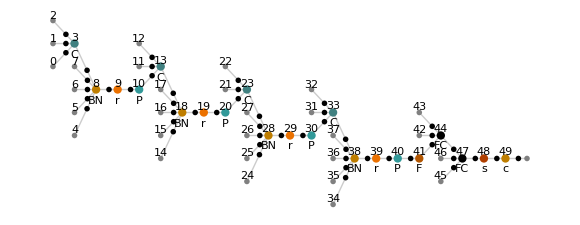

```mathematica
NetInformation[netECA19,"MXNetNodeGraphPlot"]
```

```mathematica
NetInformation[netECA19,"SummaryGraphic"]
```

-Graphics-

```mathematica
dataECA19=dataC[128,128,16384];
```

```mathematica
dataTotalistic2BigC19=genData2r2C[128,128,4096];
```

```mathematica
dataTotalistic3BigC19=data3T2C[128,128,4096];
```

```mathematica
dataTotalistic4BigC19=data4TC[128,128,4096];
```

```mathematica
dataTotalistic5BigC19=genData5TCC[128,128,16384];
```

```mathematica
fullTrainingBigC19=Join[dataECA19,dataTotalistic2BigC19,dataTotalistic3BigC19,dataTotalistic4BigC19,dataTotalistic5BigC19];
```

```mathematica
Length[fullTrainingBigC19]
```

90112

```mathematica
RandomSample[fullTrainingBigC19,20]
```

{-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2}

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/home/esilverman/Documents

```mathematica
netECA19=NetTrain[netECA19,fullTrainingBigC19,MaxTrainingRounds->200,BatchSize->256,TargetDevice->"GPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

### Generate test data for Network XIX (200 epochs)

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA19=Import["netECA19-r200.wlnet"]
```

NetChain[<>]

```mathematica
testDataECABigC=dataC[128,128,1024];
testData2TBigC=genData2r2C[128,128,1024];
testData3TBigC=data3T2C[128,128,1024];
testData4TBigC=data4TC[128,128,1024];
testData5TBigC=genData5TCC[128,128,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2}

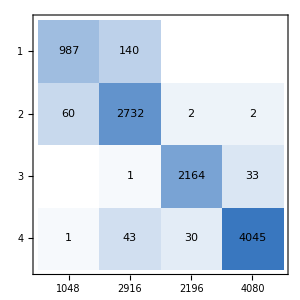
{0.969531,<|1→0.941794,2→0.9369,3→0.985428,4→0.991422|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA19, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA19[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA19[highEntBigC]]
Thread[lowEntBigC->netECA19[lowEntBigC]]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→4}

{-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→4}

### Testing Network XIX (200 epochs) on unseen CA rule spaces

#### 2-colour non-totalistic, range 2

```mathematica
test4Data2kr2C19= datak2r2C[128,128,8];
Thread[test4Data2kr2C19->netECA19[Keys@test4Data2kr2C19,{"TopProbabilities",2}]]
```

{(-Graphics-→3623639841)→{4→5.92466×10^-19,3→1.},(-Graphics-→4204902033)→{4→2.56823×10^-8,2→1.},(-Graphics-→3766586648)→{1→0.,3→1.},(-Graphics-→3083711710)→{4→2.17708×10^-25,3→1.},(-Graphics-→3912062127)→{1→0.,2→1.},(-Graphics-→3127103417)→{1→0.,3→1.},(-Graphics-→1368223734)→{3→0.0375692,4→0.962431},(-Graphics-→1157293582)→{4→0.253713,3→0.746287}}

#### 2-colour non-totalistic, range 3

```mathematica
test4Data2kr3C19 = datak2r3NT[128,128,8];
Thread[test4Data2kr3C19->netECA19[Keys@test4Data2kr3C19,{"TopProbabilities",2}]]
```

{(-Graphics-→124905465127170717525549371999495851185)→{4→4.25787×10^-22,3→1.},(-Graphics-→64150751993555644365500719311625036355)→{4→3.40968×10^-31,3→1.},(-Graphics-→36728299501322596356207863519173249151)→{4→1.92235×10^-12,3→1.},(-Graphics-→323119304778780202562738468472713800353)→{3→0.190559,4→0.809441},(-Graphics-→176137957070216127711947686257562998744)→{1→0.,3→1.},(-Graphics-→66657172551850916438827226271776823681)→{4→9.37229×10^-18,3→1.},(-Graphics-→95305147057683925587325090943101523205)→{4→1.7544×10^-26,3→1.},(-Graphics-→75507431845018814437187840734694338361)→{4→1.14088×10^-28,3→1.}}

#### 3-colour non-totalistic, range 1

```mathematica
test4Data3kr1C19 = datak3r1NT[128,128,8];
Thread[test4Data3kr1C19->netECA19[Keys@test4Data3kr1C19,{"TopProbabilities",2}]]
```

{(-Graphics-→903740772813)→{4→1.43387×10^-14,3→1.},(-Graphics-→4969181144217)→{2→0.0805151,4→0.919485},(-Graphics-→7038367528689)→{3→8.64922×10^-26,4→1.},(-Graphics-→432813174387)→{4→1.4013×10^-45,2→1.},(-Graphics-→2083475355420)→{4→1.38076×10^-8,3→1.},(-Graphics-→966244316659)→{4→8.30269×10^-33,3→1.},(-Graphics-→2855715719711)→{1→0.,3→1.},(-Graphics-→2262027167458)→{4→9.07924×10^-22,3→1.}}

#### 3-colour totalistic, range 2

```mathematica
test4Data3kr2C19 = datak3r2C[128,128,8];
Thread[test4Data3kr2C19->netECA19[Keys@test4Data3kr2C19,{"TopProbabilities",2}]]
```

{(-Graphics-→44637)→{1→0.,4→1.},(-Graphics-→97532)→{1→0.0136907,2→0.985288},(-Graphics-→81718)→{4→2.22072×10^-29,3→1.},(-Graphics-→168849)→{1→0.,4→1.},(-Graphics-→169937)→{2→0.0000493435,1→0.999913},(-Graphics-→172884)→{4→0.0000281311,3→0.999972},(-Graphics-→76127)→{4→1.65065×10^-10,3→1.},(-Graphics-→72457)→{3→0.0406162,4→0.959384}}

#### 3-colour totalistic, range 3

```mathematica
test4Data3kr3C19 = datak3r3C[128,128,8];
Thread[test4Data3kr3C19->netECA19[Keys@test4Data3kr3C19,{"TopProbabilities",2}]]
```

{(-Graphics-→5332402)→{1→0.,3→1.},(-Graphics-→12215348)→{3→0.0215091,4→0.978491},(-Graphics-→5882266)→{4→7.74599×10^-10,3→1.},(-Graphics-→3262519)→{1→0.,3→1.},(-Graphics-→4981094)→{4→0.000228014,3→0.999772},(-Graphics-→9082439)→{4→1.88074×10^-13,3→1.},(-Graphics-→1672559)→{3→0.0000689613,4→0.999931},(-Graphics-→4454413)→{3→0.152785,4→0.847215}}

#### 4-colour non-totalistic, range 1

```mathematica
test4Data4kr1C19 = datak4r1NT[128,128,8];
Thread[test4Data4kr1C19->netECA19[Keys@test4Data4kr1C19,{"TopProbabilities",2}]]
```

{(-Graphics-→268480064929651762891007015829128083689)→{4→5.90905×10^-31,3→1.},(-Graphics-→309415291386320905513458675451823606210)→{3→0.0527879,4→0.947212},(-Graphics-→30989344170865628249558072247841941742)→{4→1.13198×10^-13,3→1.},(-Graphics-→38159113987244829576355750648069816463)→{3→5.90041×10^-36,4→1.},(-Graphics-→249183157890630189577220606861906191102)→{4→5.20515×10^-10,3→1.},(-Graphics-→303528074844669290852560133934740411631)→{3→0.0369437,4→0.963056},(-Graphics-→86045152578514755153037573764695519542)→{4→9.68725×10^-27,3→1.},(-Graphics-→35725484667282961631098969929047786325)→{3→2.96151×10^-29,4→1.}}

#### 4-colour totalistic, range 2

```mathematica
test4Data4kr2C19= datak4r2C[128,128,8];
Thread[test4Data4kr2C19->netECA19[Keys@test4Data4kr2C19,{"TopProbabilities",2}]]
```

{(-Graphics-→3039279908)→{4→1.99769×10^-22,3→1.},(-Graphics-→1004857722)→{4→2.69276×10^-14,3→1.},(-Graphics-→1136086050)→{4→5.1036×10^-14,3→1.},(-Graphics-→3492358882)→{3→1.56014×10^-7,4→1.},(-Graphics-→1069866717)→{4→8.91689×10^-21,3→1.},(-Graphics-→171122738)→{4→2.21848×10^-11,3→1.},(-Graphics-→3452577709)→{4→1.17042×10^-13,3→1.},(-Graphics-→701805990)→{4→2.21188×10^-16,3→1.}}

#### 5-colour totalistic, range 1

```mathematica
test4Data5kr1C19 = data5T2C[8,128,128];
Thread[test4Data5kr1C19->netECA19[Keys@test4Data5kr1C19,{"TopProbabilities",2}]]
```

{(-Graphics-→1207540399)→{4→2.97016×10^-21,2→1.},(-Graphics-→1142383118)→{1→0.,4→1.},(-Graphics-→1123443123)→{4→0.0000133564,2→0.999987},(-Graphics-→179147268)→{3→0.00253984,4→0.99746},(-Graphics-→1070088188)→{4→5.16433×10^-17,2→1.},(-Graphics-→839709526)→{1→1.99965×10^-42,2→1.},(-Graphics-→1029145401)→{4→4.63463×10^-18,3→1.},(-Graphics-→153105290)→{3→4.82742×10^-35,4→1.}}

#### 6-colour totalistic, range 1

```mathematica
test4Data6kr1C19= data6TC[8,128,128];
Thread[test4Data6kr1C19->netECA19[Keys@test4Data6kr1C19,{"TopProbabilities",2}]]
```

{(-Graphics-→521151757166)→{4→4.2538×10^-27,3→1.},(-Graphics-→1148948615051)→{3→1.05684×10^-11,4→1.},(-Graphics-→1701138861521)→{3→0.344279,4→0.655721},(-Graphics-→772044852372)→{4→3.00861×10^-22,2→1.},(-Graphics-→401641356701)→{4→1.64612×10^-16,3→1.},(-Graphics-→1317230504887)→{3→7.00649×10^-45,4→1.},(-Graphics-→688870202959)→{2→4.08491×10^-13,4→1.},(-Graphics-→2362168351069)→{2→9.19252×10^-43,4→1.}}

#### 6-colour totalistic, range 2

```mathematica
test4Data6kr2C19 = data6T2C[8,128,128];
Thread[test4Data6kr2C19->netECA19[Keys@test4Data6kr2C19,{"TopProbabilities",2}]]
```

{(-Graphics-→148490913881245616342)→{3→6.33961×10^-15,4→1.},(-Graphics-→137813202347051710725)→{4→2.24399×10^-27,3→1.},(-Graphics-→145612570579789266485)→{4→1.52405×10^-9,3→1.},(-Graphics-→57362919586594306710)→{4→0.031388,3→0.968612},(-Graphics-→24770952214224040296)→{4→5.16516×10^-16,3→1.},(-Graphics-→143600862017240236453)→{4→1.30214×10^-22,3→1.},(-Graphics-→160410817633450677074)→{4→0.000231853,3→0.999768},(-Graphics-→99035735849117353433)→{4→7.72208×10^-20,3→1.}}

#### 7-colour totalistic, range 1

```mathematica
test4Data7kr1C19 = data7TC[8,128,128];
Thread[test4Data7kr1C19->netECA19[Keys@test4Data7kr1C19,{"TopProbabilities",2}]]
```

{(-Graphics-→7905962486151833)→{4→0.000554173,3→0.999446},(-Graphics-→5986825348569542)→{4→0.0000562114,3→0.999944},(-Graphics-→5160779372988604)→{3→1.30743×10^-8,4→1.},(-Graphics-→2668104076298035)→{4→3.94844×10^-18,3→1.},(-Graphics-→3691759700407743)→{4→4.45377×10^-16,3→1.},(-Graphics-→1440812301139250)→{4→2.17204×10^-16,3→1.},(-Graphics-→10929419536918414)→{4→0.0898063,2→0.910194},(-Graphics-→870299002890078)→{4→2.68048×10^-10,3→1.}}

#### 8-colour totalistic, range 1

```mathematica
test4Data8kr1C19= data8TC[8,128,128];
Thread[test4Data8kr1C19->netECA19[Keys@test4Data8kr1C19,{"TopProbabilities",2}]]
```

{(-Graphics-→59125043292911533831)→{4→2.29341×10^-24,3→1.},(-Graphics-→42327489577905146096)→{4→2.26592×10^-16,3→1.},(-Graphics-→27493918164619079600)→{4→1.41836×10^-22,3→1.},(-Graphics-→44604484385457579525)→{1→0.,4→1.},(-Graphics-→44601321771076613987)→{4→7.78289×10^-25,3→1.},(-Graphics-→41129731740372203883)→{3→0.274545,4→0.725455},(-Graphics-→69557501891528005051)→{4→5.60689×10^-12,3→1.},(-Graphics-→71754449283143194262)→{4→2.72879×10^-13,3→1.}}

```mathematica
test4Data8kr1C19= data8TC[8,128,128];
Thread[test4Data8kr1C19->netECA19[Keys@test4Data8kr1C19,{"TopProbabilities",2}]]
```

{(-Graphics-→30958781818328214442)→{4→4.62524×10^-15,3→1.},(-Graphics-→61018914870782867384)→{4→1.13687×10^-12,3→1.},(-Graphics-→20705257985378094677)→{4→1.82975×10^-19,3→1.},(-Graphics-→43941374463684638030)→{4→1.04552×10^-6,3→0.999999},(-Graphics-→3024227929898264848)→{4→1.85219×10^-8,3→1.},(-Graphics-→17487862603567426913)→{4→3.05308×10^-7,3→1.},(-Graphics-→63093631381744169828)→{2→1.26841×10^-29,4→1.},(-Graphics-→27830330837012619129)→{4→0.126106,3→0.873894}}

#### 8-colour totalistic, range 2

```mathematica
test4Data8kr2C19= data8T2C[8,128,128];
Thread[test4Data8kr2C19->netECA19[Keys@test4Data8kr2C19,{"TopProbabilities",2}]]
```

{(-Graphics-→147951460881093444119820865699524)→{3→1.95996×10^-6,4→0.999998},(-Graphics-→119355423761325445881228685558134)→{4→0.060776,3→0.939224},(-Graphics-→307982756305321800462830043829803)→{4→2.91468×10^-9,3→1.},(-Graphics-→62874465515649272486967493933559)→{4→5.81908×10^-7,3→0.999999},(-Graphics-→65948684565606780569516519912636)→{4→0.0000545016,3→0.999946},(-Graphics-→181374136488855143429706946971289)→{4→2.66552×10^-19,3→1.},(-Graphics-→176951646325376055797052520179269)→{4→1.80483×10^-11,3→1.},(-Graphics-→223691650274434738686390233580833)→{4→1.5659×10^-25,3→1.}}

#### 9-colour totalistic, range 1

```mathematica
test4Data9kr1C19= data9TC[8,128,128];
Thread[test4Data9kr1C19->netECA19[Keys@test4Data9kr1C19,{"TopProbabilities",2}]]
```

{(-Graphics-→650813664375243924798654)→{3→1.79014×10^-12,4→1.},(-Graphics-→693038569142680517501061)→{4→1.91095×10^-15,3→1.},(-Graphics-→172075759297755102243593)→{4→8.47525×10^-15,3→1.},(-Graphics-→635936007119328418474377)→{4→8.59589×10^-12,3→1.},(-Graphics-→83078033797966507654335)→{4→2.50512×10^-6,3→0.999997},(-Graphics-→61694440956086220642257)→{4→1.8296×10^-15,3→1.},(-Graphics-→19805866291496747949388)→{4→4.2757×10^-11,3→1.},(-Graphics-→117792334074770391492414)→{4→4.76414×10^-21,3→1.}}

```mathematica
test4Data9kr1C19= data9TC[8,128,128];
Thread[test4Data9kr1C19->netECA19[Keys@test4Data9kr1C19,{"TopProbabilities",2}]]
```

{(-Graphics-→345366264162505652483033)→{4→8.11519×10^-8,3→1.},(-Graphics-→169035156573517225784083)→{4→0.000967143,3→0.999033},(-Graphics-→241423372275813570992926)→{4→1.72993×10^-11,3→1.},(-Graphics-→323997218462529363923161)→{4→7.27233×10^-16,3→1.},(-Graphics-→274602130627677155314032)→{1→0.,4→1.},(-Graphics-→538007856396749781700396)→{4→1.82013×10^-20,3→1.},(-Graphics-→282255417383452533668794)→{4→1.74469×10^-12,3→1.},(-Graphics-→386779672558013182448702)→{4→1.71419×10^-17,3→1.}}

```mathematica
test4Data9kr1C19= data9TC[8,128,128];
Thread[test4Data9kr1C19->netECA19[Keys@test4Data9kr1C19,{"TopProbabilities",2}]]
```

{(-Graphics-→161973745861678692145183)→{4→1.92323×10^-16,3→1.},(-Graphics-→195265225475606991826639)→{1→0.,4→1.},(-Graphics-→229976304993680042622116)→{4→1.13598×10^-14,3→1.},(-Graphics-→45546192831416331168463)→{4→1.78072×10^-8,3→1.},(-Graphics-→271317841721163552341788)→{4→5.28559×10^-9,3→1.},(-Graphics-→386796588960959381307104)→{4→0.00324702,3→0.996753},(-Graphics-→13757000133048760792605)→{4→0.00048392,3→0.999516},(-Graphics-→148054017088260077744039)→{4→9.52466×10^-14,3→1.}}